### DatabaseReference[]

DatabaseReference - подключение к БД

```mathematica
gp$ref=DatabaseReference[<|
"Backend"->"PostgreSQL",
"Name"->"st190333_dblab3",
"Port"->Automatic,
"Host"->"localhost",
"Username"->"st190333_",
"Password"->"1234"
|>]
```

DatabaseReference[…]

### DatabaseConnect[ref]

DatabaseConnect - проверка успешности подключения к базе данных

```mathematica
DatabaseConnect[gp$ref]
```

Success[…]

### ref[“Connected”]

DatabaseReference[]["Connected"] - убедиться, что подключены к БД

```mathematica
gp$ref["Connected"]
```

True

### ref[{"Username", "Password", "Host", "Port", "Backend", "Name"}]

DatabaseReference[][{"Username", "Password", "Host", "Port", "Backend", "Name"}] - получить определеные свойства подключения

```mathematica
gp$ref[{"Username", "Password","Host", "Port", "Backend", "Name"}]
```

<|Username→st190333_,Password→1234,Host→localhost,Port→None,Backend→PostgreSQL,Name→st190333_dblab3|>

### RelationalDatabase[ref]

RelationalDatabase - посмотреть какие таблицы есть в БД

```mathematica
RelationalDatabase[gp$ref]
```

RelationalDatabase[…]

### EntityStore[ref], EntityStores[]

EntityStore[ref] - создаем хранилище
EntityRegister[store] - без этой функции не будет работать EntityValue
EntityStores[] - вывести хранилища

```mathematica
gp$store=EntityStore[gp$ref]
```

EntityStore[…]

```mathematica
lstTables = EntityRegister[gp$store]
```

{de_ctl_patients,de_ctl_medicines,de_doc_inspection,de_tab_inspectionmedicines,de_tab_inspectionsymptoms,de_ctl_genders,de_ctl_doctors,de_ctl_symptoms,de_ctl_diagnosis,de_ctl_inspectionplaces,de_tab_medicinesideeffects}

```mathematica
EntityStores[]
```

{EntityStore[…]}

### EntityValue[“таблица”, “EntityCount”]

EntityValue["таблица", "EntityCount"] - определяет количество записей в таблице

```mathematica
lst={{"Таблица", "Количество строк"}};
For[i=1, i<Length[lstTables],i++,
lst=Join[lst,{{lstTables[[i]],EntityValue[lstTables[[i]],"EntityCount"]}} ]
]

Grid[lst,Frame->All,Alignment->Left]
```

Таблица | Количество строк
de_ctl_patients | 53568
de_ctl_medicines | 2641
de_doc_inspection | 348228
de_tab_inspectionmedicines | 1044198
de_tab_inspectionsymptoms | 1044722
de_ctl_genders | 2
de_ctl_doctors | 14
de_ctl_symptoms | 200
de_ctl_diagnosis | 14629
de_ctl_inspectionplaces | 2

```mathematica
Print["Врачами проведены осмотры в количестве ", EntityValue["de_doc_inspection", "EntityCount"]]
```

Врачами проведены осмотры в количестве 348228

```mathematica
Print["При осмотре выясняются симптомы. В базе данных определены симптомы в количестве ", EntityValue["de_ctl_symptoms", "EntityCount"]]
```

При осмотре выясняются симптомы. В базе данных определены симптомы в количестве 200

```mathematica
Print["При осмотре ставятся диагнозы. В базе данных сузествуют диагнозы в количестве ", EntityValue["de_ctl_diagnosis", "EntityCount"]]
```

При осмотре ставятся диагнозы. В базе данных сузествуют диагнозы в количестве 14629

```mathematica
Print["В базе данных содержится информация о врачах, которых ", EntityValue["de_ctl_doctors", "EntityCount"]]
```

В базе данных содержится информация о врачах, которых 14

```mathematica
Print["В базе данных содержится информация о пациентах, которых ", EntityValue["de_ctl_patients", "EntityCount"]]
```

В базе данных содержится информация о пациентах, которых 53568

```mathematica
Print["При осмотре выделяются на лечения лекарства, которых в БД ", EntityValue["de_ctl_medicines", "EntityCount"]]
```

При осмотре выделяются на лечения лекарства, которых в БД 2641

### EntityValue[] --> используя SELECT - FROM - INNER JOIN ON

Объединить таблицу Гендеры, Пациенты и вывести поля таблиц в список Wolframe Mathematica

```mathematica
(*
SELECT
Patients.de_name,Patients.de_surname,Patients.de_patronymic,Patients.de_birthday,Patients.de_address,Genders.de_name
FROM
DE_CTL_Patients AS Patients
INNER JOIN DE_CTL_Genders AS Genders ON Genders.id=Patients.de_genderId
LIMIT 10;
*)
EntityValue[
CombinedEntityClass[
"de_ctl_genders",(*FROM DE_CTL_Genders*)
"de_ctl_patients",(*FROM DE_CTL_Patients*)
EntityFunction[{Genders, Patients},
(*
  FROM FROM DE_CTL_Genders AS Genders
INNER JOIN DE_CTL_Patients AS Patients ON Genders.id == Patients.de_genderId
*)
Genders["id"]==Patients["de_genderid"]
]
],{
EntityProperty["de_ctl_patients", "de_name"],(*SELECT DE_CTL_Patients.de_name*)
EntityProperty["de_ctl_patients", "de_surname"],(*SELECT DE_CTL_Patients.de_surname*)
EntityProperty["de_ctl_patients", "de_patronymic"],(*SELECT DE_CTL_Patients.de_patronymic*)
EntityProperty["de_ctl_patients", "de_birthday"],(*SELECT DE_CTL_Patients.de_birthday*)
EntityProperty["de_ctl_patients", "de_address"],(*SELECT DE_CTL_Patients.de_birthday*)
EntityProperty["de_ctl_genders", "de_name"] (*SELECT DE_CTL_Genders.de_name*)
}][[1;;10]]
```

{{Никита,Большаков,Матвеевич,Tue 15 Mar 1966,ул. Волгоградская д. 28,мужской},{Ольга,Некрасова,Петровна,Wed 25 Sep 1963,ул. Волгоградская д. 28,женский},{Хоселито,Кондрашов,Вахтангович,Sat 13 Mar 1976,ул. Волгоградская д. 28,мужской},{Акгюль,Собянина,Натановна,Thu 16 Dec 1926,ул. Волгоградская д. 28,женский},{Андокид,Лобанов,Антонович,Wed 9 Dec 1925,ул. Волгоградская д. 28,мужской},{Еликонида,Баранова,Прохоровна,Fri 10 May 1940,ул. Волгоградская д. 28,женский},{Джаббар,Вдовин,Владиленович,Mon 13 Aug 1990,ул. Волгоградская д. 28,мужской},{Янина,Яшина,Евдокимовна,Sat 11 May 2002,ул. Волгоградская д. 28,женский},{Досифей,Голованов,Гаджиевич,Mon 7 Dec 1953,ул. Волгоградская д. 28,мужской},{Юлия,Бабушкина,Вахтанговна,Fri 25 Feb 1927,ул. Волгоградская д. 28,женский}}

### ExternalEvaluate и BarChart

ExternalEvaluate - выполняем SQL запрос
BarChart - рисуем столбчатую диаграмму

Найти врачей, которые поставили все диагнозы

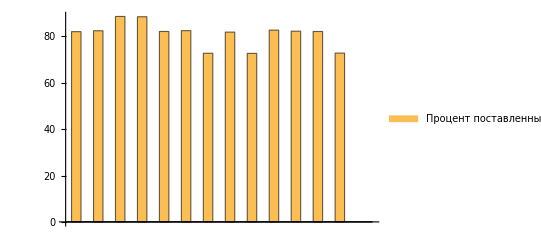

```mathematica
gp$dataProcentDiagnosis = ExternalEvaluate[gp$ref,
"SELECT
    -- = = = = = = = = = = = = = = = = Колонка \"ДанныеВрача\"
    CONCAT(
        'Участок №',
        Doctors.de_region,
        ', кабинет ',
        Doctors.de_office,
        ', ',
        Doctors.de_surname,
        ' ',
        Doctors.de_name,
        ' ',
        Doctors.de_patronymic
    ) AS ДанныеВрача,
    -- = = = = = = = = = = = = = = = = Колонка \"ПроцентПоставДиагнМира\"
    CAST( (
            CAST(УникДиагПоставлено AS FLOAT) * 100 / CAST(ВсегоДиагнозовМира AS FLOAT)
        ) AS NUMERIC(6, 3)
    ) AS ПроцентПоставДиагнМира,
    -- = = = = = = = = = = = = = = = = Колонка \"Сообщение\"
    CONCAT(
        'Поставлено ',
        УникДиагПоставлено,
        ' уникальных диагноза из ',
        ВсегоДиагнозовМира
    ) AS Сообщение
FROM (
        SELECT
            -- = = = = = = = = = = = = = = = = Колонка \"ИдДоктора\"
            de_doctorId AS ИдДоктора,
            -- = = = = = = = = = = = = = = = = Колонка \"УникДиагПоставлено\"
            COUNT(DISTINCT de_diagnosisId) AS УникДиагПоставлено,
            /* = = = = = = = = = = = = = = = = Колонка \"ВсегоДиагнозовМира\"*/ (
                SELECT
                    COUNT(*)
                FROM
                    DE_CTL_Diagnosis
            ) AS ВсегоДиагнозовМира
        FROM
            DE_DOC_Inspection
        GROUP BY
            de_doctorId
    ) AS Подзапрос
    INNER JOIN DE_CTL_Doctors AS Doctors ON Подзапрос.ИдДоктора = Doctors.id
    /*
     WHERE
     CAST( (
     CAST(УникДиагПоставлено AS FLOAT) * 100 / CAST(ВсегоДиагнозовМира AS FLOAT)
     ) AS NUMERIC(6, 3)
     ) = 100.000
     */
/*ORDER BY
    ПроцентПоставДиагнМира DESC*/;"]

gp$lst={};
For[i=0,i<Length[gp$dataProcentDiagnosis],i++,
gp$lst = Join[{{gp$dataProcentDiagnosis[[i]][2]}}, gp$lst]
]

BarChart[gp$lst,ChartLegends->{"Процент поставленных диагнозов мира врачами каждого участка"}]
```

### ExternalEvaluate и PieChart

ExternalEvaluate - выполняем SQL запрос
PieChart - рисуем груговую диаграмму

Найти сколько мужчин были обслужанных на дому на каждом участке

```mathematica
gp$resPeoplesInHome =ExternalEvaluate[gp$ref,
"SELECT
    -- = = = = = = = = = = = = = = = = Колонка \"ИдВрача\"
    Doctors.id AS ИдВрача,
    -- = = = = = = = = = = = = = = = = Колонка \"ДанныеВрача\"
    CONCAT(
        'Участок ',
        Doctors.de_region,
        ', кабиент ',
        Doctors.de_office,
        ', ',
        Doctors.de_surname,
        ', ',
        Doctors.de_name,
        ', ',
        Doctors.de_patronymic
    ) AS ДанныеВрача,
    -- = = = = = = = = = = = = = = = = Колонка \"ГендерПациента\"
    Genders.de_name AS ГендерПациента,
    -- = = = = = = = = = = = = = = = = Колонка \"МестоОсмотра\"
    Places.de_name AS МестоОсмотра,
    -- = = = = = = = = = = = = = = = = Колонка \"КолвоПациентовОбслужЗаПериод\"
    COUNT(Patients.id) AS КолвоПациентовОбслужЗаПериод
FROM
    DE_DOC_Inspection AS Inspections
    INNER JOIN DE_CTL_Patients AS Patients ON Patients.id = Inspections.de_patientId
    INNER JOIN DE_CTL_Genders AS Genders ON Genders.id = Patients.de_genderId
    INNER JOIN DE_CTL_InspectionPlaces AS Places ON Places.id = Inspections.de_placeId
    INNER JOIN DE_CTL_Doctors AS Doctors ON Doctors.id = Inspections.de_doctorId
WHERE
    Inspections.de_startTime > '2019-01-01 00:00:00' AND Places.de_name = 'на дому' AND Genders.de_name LIKE 'мужской'
GROUP BY
    Doctors.id,
    CONCAT(
        'Участок ',
        Doctors.de_region,
        ', кабиент ',
        Doctors.de_office,
        ', ',
        Doctors.de_surname,
        ', ',
        Doctors.de_name,
        ', ',
        Doctors.de_patronymic
    ),
    Genders.de_name,
    Places.de_name
ORDER BY ИдВрача;"
]

gp$lst = {};
gp$lst2 = {};
For[i=1, i<Length[gp$resPeoplesInHome ],i++,
gp$lst=Join[gp$lst,{gp$resPeoplesInHome [[i]][[5]]}];
gp$lst2=Join[gp$lst2,{gp$resPeoplesInHome [[i]][[2]]}];
]

PieChart[gp$lst, ChartLegends->gp$lst2, ChartStyle->"DarkRainbow"]
```

-Graphics-

### DatabaseDisconnect[ref]

DatabaseDisconnect[ref] - отключиться от базы данных

```mathematica
DatabaseDisconnect[gp$ref]
```

Success[…]

Литература:
- https://reference.wolfram.com/language/guide/WorkingWithRelationalDatabases.html
- https://reference.wolfram.com/language/tutorial/RelationalDatabasesQuickStart.html#2047181595

### Wolfram Alpha в свободной форме математические уравнения

WolframAlphaQueryParseResults

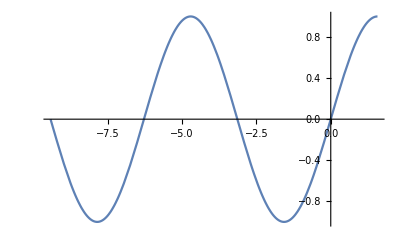

WolframAlphaQueryParseResults

1

### Wolfram Alpha об химических элемента

WolframAlphaQueryResults

oxygen

### Wolfram Alpha об цвете

WolframAlphaQueryResults

RGBColor[1, 1, 0]